```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Inside Nonlinear Filters

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Many image processing filters operate by applying some function to all the pixels in a local neighborhood around each pixel. For instance, the MeanFilter[ ] takes the average value of all the pixels in the neighborhood, and there are a number of named (built-in) image filters which apply specific functions to the pixels in the neighborhood. Depending on the details of the function, the filter may be linear or nonlinear. In either case, the radius parameter defines the size of the neighborhood and as the parameter increases, the effect becomes more pronounced.

```mathematica
TableForm[{{Hyperlink["fAdaptThresh",{"vvNonlinearFilters.nb","labelfAdaptThresh"},BaseStyle->mathColor],labelfAdaptThresh},{Hyperlink["RGBRand",{"vvNonlinearFilters.nb","labelRGBRand"},BaseStyle->mathColor],labelRGBRand},{Hyperlink["RGBSeparate",{"vvNonlinearFilters.nb","labelRGBSeparate"},BaseStyle->mathColor],labelRGBSeparate},{Hyperlink["GenConv",{"vvNonlinearFilters.nb","labelGenConv"},BaseStyle->mathColor],labelGenConv},{Hyperlink["Jitter",{"vvNonlinearFilters.nb","labelJitter"},BaseStyle->mathColor],labelJitter}}]
```

| A variation on adaptive thresholding
based on the local character of the image
 | Every pixel is converted to a pure R, pure G, or pure B value
 | Using RGB channels separately to calculate the output
 | Generalized convolution with a variety of nonlinear functions
 | Jitter moves the pixels around locally in a random way

There are a large collection of built-in filters in most image processing languages: some of Mathematica’s are

```mathematica
?*Filter
```

and one or some combination of these may well accomplish a given image processing task. But sometimes it is necessary to go further. This notebook begins by showing how the ImageFilter[ ] command can be used to create a large variety of filters via a user-defined function f[ ] (the first argument) and then proceeds to discuss the most general construct using the (nonlinear options in the) ListConvolve[ ] and/or ListCorrelate[ ] functions to create almost any conceivable local filter. The help file for ImageFilter[ ] begins

```mathematica
?ImageFilter
```

RowBox[{"ImageFilter", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["image", "TI"], ",", StyleBox["r", "TI"]}], "]"}] applies the function StyleBox["f", "TI"] to the range-StyleBox["r", "TI"] neighborhood of each pixel in each channel of StyleBox["image", "TI"].

To see how this works in a simple setting, the first example recreates the MeanFilter[ ] using the function fMean[ ] which flattens the input matrix into a list, sums the elements, and then divides by the number of elements. Since this is just calculating the mean of the elements in the neighborhood, the output is identical to the built-in meanFilter[ ].

```mathematica
img = allImagesColor[[vanTreeRoots]];
fMean[x_]:=Total[Flatten[x]]/Length[Flatten[x]];
Labeled[GraphicsRow[{ImageFilter[fMean,img,7],MeanFilter[img,7]},AspectRatio->1/2,ImageSize->600],"Duplicating the effect of the MeanFilter[] using the more general ImageFilter[]",LabelStyle->captionStyle]
```

-Graphics-Duplicating the effect of the MeanFilter[] using the more general ImageFilter[]

The RangeFilter[ ] assigns the difference between the maximum and the minimum in the neighborhood to each pixel. This example mimics the effect of the RangeFilter[ ] by creating a user specified function fRange[ ] that carries out the desired processing when called by the ImageFilter[ ] command.

```mathematica
fRange[x_]:=Max[Flatten[x]]-Min[Flatten[x]];
Labeled[GraphicsRow[{ImageFilter[fRange,img,7],RangeFilter[img,7]},AspectRatio->1/2,ImageSize->600],"Approximating the effect of the RangeFilter[] using the more general ImageFilter[]",LabelStyle->captionStyle]
```

-Graphics-Approximating the effect of the RangeFilter[] using the more general ImageFilter[]

In the introduction to nonlinear filters, an adaptive thresholding algorithm was presented which changes based on the context; it finds the mean value in each neighborhood and sets the pixel to white if it is greater than threshold*mean, and otherwise sets it to black. Here’s a variation that finds the mean value in the neighborhood; if the pixel is greater than threshold*mean, leave the pixel value alone, otherwise set it to black.

```mathematica
labelfAdaptThresh="A variation on adaptive thresholding\nbased on the local character of the image";
infofAdaptThresh="This adaptive method finds the mean value in each neighborhood. If the pixel value is greater than threshold*mean, the pixel retains its value, otherwise it is set to black.\n\nThis implementation has two controls: the size of the neighborhood and the threshold.\n\nThe operation of the algorithm is defined by the function fAdaptThresh[ ].\n\nFor grayscale images, this can nicely separate the thread peaks from the valleys.\n\nFor color images it can help to accentuate edges by suppressing small-valued pixels (where small can be safely interpreted locally, within the neighborhood).";
fAdaptThresh[x_,threshRat_]:=Module[{center,meanX,thisPix},
y=x;
meanX=Mean[Flatten[x]];
center=Floor[Sqrt[Length[Flatten[x]]]/2];
thisPix=x[[center,center]];
Boole[thisPix>threshRat meanX] thisPix];
Row[{Manipulate[Image[ImageFilter[fAdaptThresh[#,tau]&,ImageTake[allImagesXray[[i]],{1,200},{1,200}],n],ImageSize->300],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],info[infofAdaptThresh]}],
{{n,3,"neighborhood"},1,30,1},
{{tau,1,"threshold ratio"},0.9,1.1},
FrameLabel->Style[labelfAdaptThresh,Medium],ContinuousAction->False,TrackedSymbols->{i,n,tau},SaveDefinitions->saveDef], Spacer[20],
Manipulate[Image[ImageFilter[fAdaptThresh[#,tau]&,ImageTake[allImagesColor[[i]],{1,200},{1,200}],n],ImageSize->300],Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infofAdaptThresh]}],{{n,3,"neighborhood"},1,30,1},{{tau,1,"threshold ratio"},0.9,1.1},
FrameLabel->Style[labelfAdaptThresh,Medium],ContinuousAction->False,
TrackedSymbols->{i,n,tau},SaveDefinitions->saveDef]}]
```

The basic syntax of these filters is the same. The ImageFilter[ ] command has three arguments: the name of a function that will be called, the image to be processed, and the size of the neighborhood. The function can be anything, but it must have correct number of inputs and outputs: the input is a matrix of size 2r+1 by 2r+1 where r is the neighborhood size parameter, the output is a scalar. If there is only the one input to the function (as in the fRange[ ] example above) then it can be called simply as ImageFilter[fRange, image, neighborhood]. If there are extra arguments, these can be distinguished from the image data matrix using the pure function symbols # and & as in the fAdaptThresh[ ] example above, which is called using ImageFilter[fAdaptThresh[#, tau] &, image, neighborhood]. By default, the function is called separately for each of the RGB channels of a multichannel image. This default can be changed using the Interleaving->True option, in which case the function passed the RGB channel values. A simple example of this is turns an image to grayscale by averaging the RGB pixel values.

```mathematica
img=allImagesColor[[vanTreeRoots]];
fGrayscale[x_]:=Module[{},Total[Flatten[x]]/Length[Flatten[x]]];
Labeled[GraphicsRow[{ImageFilter[fGrayscale,img,0,Interleaving->True],ColorConvert[img,"Grayscale"]},AspectRatio->1/2,ImageSize->600],"Duplicating the effect of the ColorConvert[] using the more general ImageFilter[]",LabelStyle->captionStyle]
```

-Graphics-Duplicating the effect of the ColorConvert[] using the more general ImageFilter[]

With this option, the function must take as input a 2r+1 by 2r+1 by 3 matrix. The subtle differences in the outputs show that the built in ColorConvert[ ] is not just doing simple averaging of the RGB values, but instead weights them unequally. To emphasize the generality of the process, here is a filter that looks at each RGB value and assigns a pure R, pure G, or a pure B color with probability proportional to the RGB values. The output is now a RGB 3-vector.

```mathematica
labelRGBRand="Every pixel is converted to a pure R, pure G, or pure B value";
infoRGBRand="This filter looks at each RGB value and assigns a pure R, pure G, or a pure B color with probability proportional to the RGB values.";
fPureRGB[x_]:=Module[{z},z=Flatten[x];
If[Total[z]==0,{0,0,0},
RandomChoice[z/Total[z]->z{{1,0,0},{0,1,0},{0,0,1}}]]];
Manipulate[ImageFilter[fPureRGB,ImageResize[allImagesColor[[i]],{500}],0,Interleaving->True],Row[{Control[{{i,vanGarden,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoRGBRand]}],
FrameLabel->Style[labelRGBRand,Medium],SynchronousUpdating->False,TrackedSymbols->{i},SaveDefinitions->saveDef]
```

HW: As written, fPureRGB[ ] only works for a neighborhood of size 0. Create a more general function that bases the probability of getting a pure R, pure G, or pure B on larger neighborhoods.

A more practical use of the Interleaving-> option is to process the R, G and B planes separately. This can often be useful when trying to isolate particular parts of an image for further processing. This example sets the output pixel to Abs[ Max[R]-Min[R]+Max[G]-Min[G]+Max[B]-Min[B] ] over each 2r+1 by 2r+1 block where R, G and B represent the red, green, and blue channels respectively. If the output is a scalar (as here) the output image will be displayed as grayscale (even though it is calculated from the RGB channels).

```mathematica
labelRGBSeparate="Using RGB channels separately to calculate the output";
infoRGBSeparate="This filter processes the R, G and B channels separately. This can be useful when trying to isolate particular parts of an image for further processing.\n\nThe filter sets the output pixel to Abs[ Max[R]-Min[R]+Max[G]-Min[G]+Max[B]-Min[B] ] over each 2r+1 by 2r+1 block where R, G and B represent the red, green, and blue channels respectively.\n\nSince the output is a scalar, the image will be displayed as a grayscale image.\n\nWith small neighborhoods, the resulting images are something like a pencil sketch.\n\nWith larger neighborhoods, the resulting images have fat dark outlines at many important edges.";
fMaxAbsRG[x_]:=Module[{ker,allRs,allGs},
ker=Flatten[x,1];
allRs=ker[[All,1]];
allGs=ker[[All,2]];
allBs=ker[[All,3]];
Abs[(Max[allRs]-Min[allRs]+Max[allGs]-Min[allGs]+Max[allBs]-Min[allBs])/3]];
Manipulate[ColorNegate[ImageAdjust[ImageFilter[fMaxAbsRG,ImageResize[allImagesColor[[i]],{400}],n,Interleaving->True]]],Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoRGBSeparate]}],
{{n,1,"neighborhood"},1,10,1},SynchronousUpdating->False,ContinuousAction->False,
FrameLabel->Style[labelRGBSeparate,Medium],ContinuousAction->False,TrackedSymbols->{i,n},SaveDefinitions->saveDef]
```

### Nonlinear Filtering with Generalized Inner Product

There is a complete and compelling theory for linear filters that helps implement and design filters for specific tasks, mainly through use of the Fourier spectrum. Such filters use a "mask" (or impulse response, or kernel) and convolve with the image. The tool of choice for this is:

```mathematica
?ListConvolve
```

RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"]}], "]"}] forms the convolution of the kernel StyleBox["ker", "TI"] with StyleBox["list", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["k", "TI"]}], "]"}] forms the cyclic convolution in which the StyleBox["k", "TI"]SuperscriptBox["", "th"] element of StyleBox["ker", "TI"] is aligned with each element in StyleBox["list", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]]}], "}"}]}], "]"}] forms the cyclic convolution whose first element contains RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", "1", "]"}], "]"}], RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["L", "TI"]], "]"}], "]"}]}] and whose last element contains RowBox[{RowBox[{StyleBox["list", "TI"], "[", RowBox[{"[", RowBox[{"-", "1"}], "]"}], "]"}], RowBox[{StyleBox["ker", "TI"], "[", RowBox[{"[", SubscriptBox[StyleBox["k", "TI"], StyleBox["R", "TI"]], "]"}], "]"}]}]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["p", "TI"]}], "]"}] forms the convolution in which StyleBox["list", "TI"] is padded at each end with repetitions of the element StyleBox["p", "TI"]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] forms the convolution in which StyleBox["list", "TI"] is padded at each end with cyclic repetitions of the SubscriptBox[StyleBox["p", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"]}], "]"}] forms a generalized convolution in which StyleBox["g", "TI"] is used in place of Times and StyleBox["h", "TI"] in place of Plus. 
RowBox[{"ListConvolve", "[", RowBox[{StyleBox["ker", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["klist", "TI"], ",", StyleBox["padding", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["h", "TI"], ",", StyleBox["lev", "TI"]}], "]"}] forms a convolution using elements at level StyleBox["lev", "TI"] in StyleBox["ker", "TI"] and StyleBox["list", "TI"].

For instance, a random matrix can be convolved with a 3x3 mask of all 1/9's to average (low pass) the image.

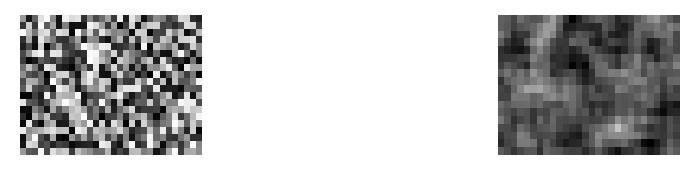
-Graphics-The image on the left is convolved with the mask in the middle to give the output on the right

```mathematica
randMat:=RandomReal[{0,1},{20,30}];
mask=ConstantArray[1/9,{3,3}];
Labeled[GraphicsRow[{ArrayPlot[randMat],MatrixForm[mask],ArrayPlot[ListConvolve[mask,randMat]]},ImageSize->700],"The image on the left is convolved with the mask in the middle to give the output on the right",LabelStyle->captionStyle]
```

Such linear filtering is only the simplest use of the ListConvolve[ ] function. Observe that there are several optional arguments, including the possibility of replacing the Times[ ] function with some user specified function g[ ] and of replacing Plus[ ] with some user specified function h[]. Think about this for a minute: instead of combining the kernel and the image by multiplying and then summing, they can be combined other ways. The first of these images shows that Times and Plus really are the default (the left hand image below is the same as the right hand image above). The middle image replaces Times with Max and Plus with Min. The right hand convolution uses Min instead of Times and Times instead of Plus!

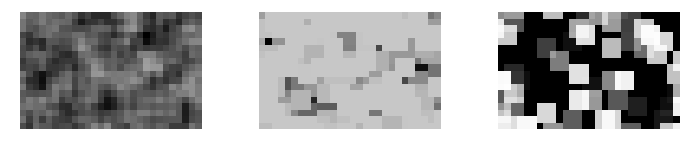
-Graphics-Linear filtering vs. two nonlinear filters, all implemented using ListConvolve[ ]

```mathematica
Labeled[GraphicsRow[{ArrayPlot[ListConvolve[mask,randMat,{-1,1},0,Times,Plus]],ArrayPlot[ListConvolve[mask,randMat,{-1,1},0,Max,Min]],ArrayPlot[ListConvolve[mask,randMat,{-1,1},0,Min,Times]]},ImageSize->700],"Linear filtering vs. two nonlinear filters, all implemented using ListConvolve[ ]",LabelStyle->captionStyle]
```

HW: The morphological operations of dilation and erosion can be defined and implemented using ListConvolve[ ] (and it’s companion ListCorrelate[ ]). In erosion, the output g(x,y) of the morphological operation at the point (x,y) is “1” if every point in the neighborhood is “1” and is zero otherwise. In dilation, the output g(x,y) of the morphological operation at the point (x,y) is the “1” if any point in the neighborhood is “1” and is zero otherwise. Given an image B and a structuring element A, here are some possibilities. For each of the possibilities, determine whether it is implementing dilation or erosion.  (a)  ListConvolve[B, A, 2, -∞, Plus, Max]; (b) ListCorrelate[-B, A, 2, ∞, Plus, Min]; (c) ListCorrelate[1 - B, A, 2, 1, BitOr, BitAnd]; (d) ListConvolve[B, A, 2, 0, BitAnd, BitOr];

HW: Show how to implement opening and closing using ListCorrelate[ ] and/or ListConvolve[ ].

Think about what is happening in the ListConvolve[ ] command. A "normal" linear convolution multiplies terms together and then sums the results. For instance, say the mask consisted of three terms [m1, m2, m3] and the image was [f1, f2, f3, f4, f5]. The convolution is then:

```mathematica
m={m1,m2,m3};
f={f1,f2,f3,f4,f5};
ListConvolve[m,f]
```

{f3 m1+f2 m2+f1 m3,f4 m1+f3 m2+f2 m3,f5 m1+f4 m2+f3 m3}

Focus, for example, on the first term of this convolution

```mathematica
ListConvolve[m,f][[1]]
```

f3 m1+f2 m2+f1 m3

Internally, this is represented (using FullForm[ ]) as

```mathematica
FullForm[ListConvolve[m,f][[1]]]
```

Plus[Times[f3,m1],Times[f2,m2],Times[f1,m3]]

What the general version of ListConvolve[] is doing, then, is to go into this FullForm[ ] and to replace all the occurrences of Times[ ] with the specified function g[ ] and to replace all occurrences of the Plus[ ] function with the specified h[ ]. We could do this manually, of course:

```mathematica
FullForm[ListConvolve[m,f][[1]]]//.{Times->g,Plus->h}
```

h[g[f3,m1],g[f2,m2],g[f1,m3]]

Picking specific functions for the g[ ] and h[ ] does exactly what you think it should.

```mathematica
FullForm[ListConvolve[m,f][[1]]]//.{Times->Max,Plus->Min}
```

Min[Max[f1,m3],Max[f2,m2],Max[f3,m1]]

ListConvolve[ ] does this automatically throughout the full calculation

```mathematica
ListConvolve[m,f,{-1,1},0,g,h]
```

{h[g[m3,f1],g[m2,f2],g[m1,f3]],h[g[m3,f2],g[m2,f3],g[m1,f4]],h[g[m3,f3],g[m2,f4],g[m1,f5]]}

Specifically using Max[ ] and Min[ ], for instance, yields.

```mathematica
ListConvolve[m,f,{-1,1},0,Max,Min]
```

{Min[Max[f1,m3],Max[f2,m2],Max[f3,m1]],Min[Max[f2,m3],Max[f3,m2],Max[f4,m1]],Min[Max[f3,m3],Max[f4,m2],Max[f5,m1]]}

The beauty of symbolic computation like this is that it is not necessary to use built-in functions. Any function (that has the correct domain and range) can be used:

```mathematica
g=Max;
h[x__]:=2 x^2;
ListConvolve[m,f,{-1,1},0,g,h]
```

{2 Max[f1,m3]^(Max[f2,m2]^(Max[f3,m1]^2)),2 Max[f2,m3]^(Max[f3,m2]^(Max[f4,m1]^2)),2 Max[f3,m3]^(Max[f4,m2]^(Max[f5,m1]^2))}

Note the double underscore above in the definition of h[ ]. This allows the function to accept a sequence of one or more expressions as its domain. Dimensionally g[ ] and h[ ] are constrained so that 
            g[ ] needs to take in (at least) two inputs and to give an n-D output
	h[ ] needs to take in any number of n-D inputs (from g[ ]) and to give a scalar output

```mathematica
Clear[g,h];
g[x_,y_]:=x^y;
h[x__]:={x}.{x};
ListConvolve[m,f,{-1,1},0,g,h]
```

{m1^(2 f3)+m2^(2 f2)+m3^(2 f1),m1^(2 f4)+m2^(2 f3)+m3^(2 f2),m1^(2 f5)+m2^(2 f4)+m3^(2 f3)}

Note the curly brackets inside the definition of h[ ]. This takes the two arguments that are input into the function h[ ] and turns them into a single list so that h[ ] has the correct number of inputs. With these same g[ ] and h[ ],

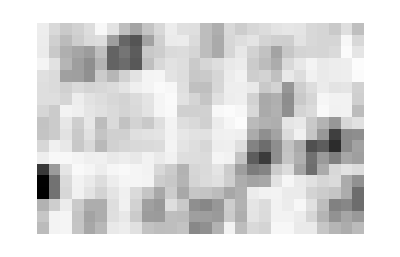

```mathematica
gXY[x_,y_]:=x^y;
hXdotX[x__]:={x}.{x};
ArrayPlot[ListConvolve[mask,randMat,{-1,1},0,gXY,hXdotX]]
```

```mathematica
labelGenConv="Generalized convolution with a variety of nonlinear functions";
infoGenConv="This implementation of generalized convolution allows choice of many ways of combining the signal and the neighborhood.\n\nChoosing g=Times and h=Plus is regular (linear) convolution.\n\nAll other choices lead to nonlinear filters.\n\nChoosing g=Plus and h=Max is dilation.\n\nChoosing g=Plus and h=Min is erosion.\n\nMost of the rest of the combinations don't have names.\n\nGeneralized convolution is so general, it's hard to imagine all the possibilities.";
gTot[x__]:=Total[{x}^2];
hSin[x__]:=Total[Sin[{x}]];
gSTD[x__]:=StandardDeviation[{x}];
hSTD[x__]:=StandardDeviation[{x}]^0.4;
gXY[x_,y_]:=x^y;
gXYInv[x_,y_]:=x^(1/(y+0.01));
hXdotX[x__]:={x}.{x};
Manipulate[ImageAdjust[Image[ListConvolve[ConstantArray[1/9,{3,3}],ImageData[ImageTake[allImagesXray[[i]],{1,250},{1,250}]],{-1,1},0,g,h]]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],info[infoGenConv]}],
{{g,Times},{gTot,gSTD,gXY,gXYInv,Min,Times,Plus}},{{h,Plus},{hSin,hSTD,hXdotX,Max,Times,Plus}},FrameLabel->Style[labelGenConv,Medium],TrackedSymbols->{i,g,h},SaveDefinitions->saveDef]
```

ListConvolve[ ] is so general, it's hard to imagine all the possibilities, since just about any functions can be used. For instance, a random function picking out one pixel value from each 2r+1 by 2r+1 block imposes a kind of digital jitter on the image. This one operates on the red, green, and blue channels separately.

```mathematica
labelJitter="Jitter moves the pixels around locally in a random way";
infoJitter="This filter implements a jitter function that picks one pixel randomly from each 2r+1 by 2r+1 block neighborhood, operating on the red, green, and blue channels separately.\n\nControl the neighborhood size wioth the slider: larger values introduce more jitter.";
hJitter[x__]:=RandomChoice[{x}];
Manipulate[{imgR,imgG,imgB}=ImageData/@ColorSeparate[ImageResize[allImagesColor[[i]],{400}]];
ColorCombine[{Image[ListConvolve[ConstantArray[1,{n,n}],imgR,{-1,1},0,Times,hJitter]],Image[ListConvolve[ConstantArray[1,{n,n}],imgG,{-1,1},0,Times,hJitter]],Image[ListConvolve[ConstantArray[1,{n,n}],imgB,{-1,1},0,Times,hJitter]]}],Row[{Control[{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoJitter]}],{{n,4,"size of jitter"},1,20,1},FrameLabel->Style[labelJitter,Medium],SynchronousUpdating->False,ContinuousAction->False,TrackedSymbols->{i,n},SaveDefinitions->saveDef]
```

The real problem with nonlinear filters is that there are too many options, and not enough understanding of how to organize everything so that the results of the operations can be predictable and comprehensible. But -- just because we can't organize everything, does not imply that we can't understand pieces of the puzzle. The idea of keeping the structure the same and using different functions (i.e., the structure of convolution yet replacing “Plus” and “Times” with user defined operations) is a powerful general principle that can be applied in many places in Mathematica. For instance, the ListCorrelate[ ] function has exactly the same options as ListConvolve[ ]. The Outer[ ] function (a generalized outer product) allows replacement of “Times” with a user defined function, and Inner[ ] (the generalized inner product) allows replacement of both “Plus” and “Times.” Similarly, ImageFilter[ ] and ImageApply[ ] allow any function to be applied directly to image data. In fact, even when the language does not explicitly encourage such uses, it is easy enough to do it yourself. The key idea is that function names are nothing special; they are like any other expression, and can be operated on, replaced, or manipulated as if they were themselves variables. For instance, say the function gg[ ] is defined as:

```mathematica
gg[x_]:=(1-x)^10
```

Then it is possible to evaluate an expression using an undefined function ff[ ] by "replacing it" (temporarily) with the function gg[ ].

```mathematica
ff[x]+ff[1-x]/.ff->gg
```

(1-x)^10+x^10

Of course, ff[ ] could be replaced by anything else at a later time, such as Log or Plus

```mathematica
ff[x]+ff[1-x]/.ff->Log
```

Log[1-x]+Log[x]

```mathematica
ff[x]+ff[1-x]/.ff->Plus
```

1

And if we want to be really silly, we can replace Plus with Times. This does two things: it replaces the “+“ operation that lies between ff[x] and ff[1-x] with a multiplication. It also replaces “1-x” with “-x”. Can you figure out why? Use the FullForm function to peek inside and see how the internal representation works.

```mathematica
ff[x]+ff[1-x]/.Plus->Times
```

ff[-x] ff[x]

This will be become clearer using the FullForm function to peek inside and see how the internal representation works.

```mathematica
FullForm[1-x]
```

Plus[1,Times[-1,x]]